# Efficiency trading

## Observable definition

```mathematica
SimpleReturns[prices_, lag_:1]:= Drop[prices, lag] - Drop[prices, -lag];
Returns[prices_, lag_:1]:= N[Log[Drop[prices,lag]]-Log[Drop[prices,-lag]]];

FirstSign[returnsSign_]:=Block[{firstSign},
firstSign = First[returnsSign];
If[firstSign ≠ 0,
Return[firstSign]
,
Return[FirstCase[returnsSign,1|-1]]
];
];
FixFirstSign[returnsSign_]:=Block[{result},
result = returnsSign;
result[[1]] = FirstSign[returnsSign];
Return[result]
];
FixAllSigns[returnsSign_]:=FixedPoint[
Flatten[SequenceReplace[#,{x_,0}:>{x,x}]]&,
FixFirstSign[returnsSign]
];

TrendDuration[prices_] := Map[Length, Split[FixAllSigns[Sign[SimpleReturns[prices]]]]];
UpwardTrendDuration[prices_] := Module[{splitted,posTrends},
	splitted = Split[FixAllSigns[Sign[SimpleReturns[prices]]]];
	posTrends = Select[splitted, Apply[And, Positive[#]]&];
	Return[Map[Length, posTrends]];
];
DownwardTrendDuration[prices_] := Module[{splitted,negTrends},
	splitted = Split[FixAllSigns[Sign[SimpleReturns[prices]]]];
	negTrends = Select[splitted, Apply[And, Negative[#]]&];
	Return[Map[Length, negTrends]];
];

TrendReturns[prices_] := Block[{endpoints},
	endpoints = Map[First, TakeList[prices, Append[TrendDuration[prices], All]]];
	Return[Returns[endpoints]];
];

DatedSimpleReturns[dates_, prices_, lag_:1] := Transpose[{Drop[dates, -1], N[Drop[prices, lag] - Drop[prices, -lag]]}];
DatedSimpleReturns[datedprices_, lag_:1] := DatedSimpleReturns[datedprices[[All, 1]], datedprices[[All, 2]], lag];

DatedReturns[dates_, prices_, lag_:1] := Transpose[{Drop[dates, -1], N[Log[Drop[prices, lag]] - Log[Drop[prices, -lag]]]}];
DatedReturns[datedPrices_, lag_:1] := DatedReturns[datedPrices[[All, 1]], datedPrices[[All, 2]], lag];

DatedTrendReturns[dates_, prices_] := Block[{endpoints},
	endpoints = Map[First, TakeList[Transpose[{dates, prices}], Append[TrendDuration[prices], All]]];
	Return[Transpose[{Drop[endpoints[[All,1]], -1], Returns[endpoints[[All, 2]]]}]];
];
DatedTrendDuration[dates_, prices_] := Block[{endpoints,trendDuration},
	trendDuration = TrendDuration[prices];
	endpoints = Map[First, TakeList[dates, Append[trendDuration, All]]];
	Return[Transpose[{Drop[endpoints, -1], trendDuration}]];
];
DatedTrendDuration[datedprices_] := Block[{endpoints,trendDuration},
	trendDuration = TrendDuration[datedprices[[All, 2]]];
	endpoints = Map[First, TakeList[datedprices[[All, 1]], Append[trendDuration, All]]];
	Return[Transpose[{Drop[endpoints, -1], trendDuration}]];
];
```

```mathematica
DivReturns[prices_]:=Drop[prices,1]/Drop[prices,-1];
PercentageReturns[prices_]:=100*(Drop[prices,1]/Drop[prices,-1]-1) ;
```

```mathematica
StandardErrorAvg[data_]:=N[StandardDeviation[data]/(√Length[data])];
MeanWithError[data_]:=ToString[TraditionalForm[Mean[data]]]<>"±"<>ToString[StandardErrorAvg[data]];
```

## Dataset loader

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Libraries","AdvancedMapping.wl"}]];
```

```mathematica
$YahooFinSession = Null;
StartYahooFin[]:=Block[{},
$YahooFinSession = StartExternalSession["Python"];

ExternalEvaluate[$YahooFinSession,"import sys"];
ExternalEvaluate[$YahooFinSession,<|"Command"->"sys.path.insert","Arguments"->{1,NotebookDirectory[]}|>];

ExternalEvaluate[$YahooFinSession,"from yahoo_fin import stock_info as si"];
ExternalEvaluate[$YahooFinSession,"from yahoo_fin import options"];
];
EndYahooFin[]:=DeleteObject[$YahooFinSession];

ToPythonDate[date_]:=DateString[date,{"Month", "/","Day","/","Year"}];
GetData[ticker_,startDate_,endDate_,indexAsDate_,interval_]:=Block[{},
If[$YahooFinSession ===Null,StartYahooFin[]];
ExternalEvaluate[$YahooFinSession,<|"Command"->"si.get_data","Arguments"->{ticker,startDate,endDate,indexAsDate,interval}|>]
];
GetIntradayData[ticker_]:=GetData[ticker,None,None,False,"1m"];
GetDailyData[ticker_,startDate_,endDate_]:=GetData[ticker,ToPythonDate[startDate],ToPythonDate[endDate],False,"1d"];
GetDailyData[ticker_,days_]:=GetDailyData[ticker,Today-Quantity[days,"Days"],Today];
```

```mathematica
FormatRawDataset[dataset_]:=Block[{rawNormal,dates,open,high,low,close,volume,formatted},
rawNormal = Values[Normal[dataset]];
dates = Map[DateString[#, {"Year", "-","Month","-","Day"}]&,rawNormal[[All,"date"]]];
open = rawNormal[[All,"open"]];
high = rawNormal[[All,"high"]];
low = rawNormal[[All,"low"]];
close = rawNormal[[All,"close"]];
volume = rawNormal[[All,"volume"]];

formatted = Prepend[Transpose[{dates,open, high,low,close,volume}],{"date","open","high","low","close","volume"}];

DeleteCases[formatted,x_/;MemberQ[x,Indeterminate]]
];
```

### Download tickers

```mathematica
GetTickerData[ticker_] := FormatRawDataset[GetDailyData[ticker,DateObject[{2010,1,1}],Today]];

DownloadTickerData[ticker_,directory_]:=Block[{data,path},
data = GetTickerData[ticker];
path = FileNameJoin[{NotebookDirectory[],directory}];
If[!DirectoryQ[path],CreateDirectory[path]];

Export[FileNameJoin[{path,ticker<>".csv"}],data]
];
```

Download dataset if not already present

```mathematica
If[!DirectoryQ[FileNameJoin[{NotebookDirectory[],"SP500"}]],
Block[{spTickers},
spTickers = {"AAL","AAP","AAPL","ABBV","ABC","ABMD","ABT","ACN","A","ADBE","ADI","ADM","ADP","ADSK","AEE","AEP","AES","AFL","AIG","AIV","AIZ","AJG","AKAM","ALB","ALGN","ALK","ALL","ALLE","ALXN","AMAT","AMD","AME","AMGN","AMP","AMT","AMZN","ANET","ANSS","ANTM","AON","AOS","APA","APD","APH","APTV","ARE","ATO","ATVI","AVB","AVGO","AVY","AWK","AXP","AZO","BAC","BA","BAX","BBY","BDX","BEN","BF-B","BIIB","BIO","BK","BKNG","BKR","BLK","BLL","BMY","BR","BRK-B","BSX","BWA","BXP","CAG","CAH","CAT","CB","CBOE","CBRE","CCI","CCL","C","CDNS","CDW","CE","CERN","CF","CFG","CHD","CHRW","CHTR","CI","CINF","CL","CLX","CMA","CMCSA","CME","CMG","CMI","CMS","CNC","CNP","COF","COG","COO","COP","COST","CPB","CPRT","CRM","CSCO","CSX","CTAS","CTLT","CTSH","CTVA","CTXS","CVS","CVX","DAL","D","DD","DE","DFS","DG","DGX","DHI","DHR","DISCA","DISCK","DIS","DISH","DLR","DLTR","DOV","DOW","DPZ","DRE","DRI","DTE","DUK","DVA","DVN","DXC","DXCM","EA","EBAY","ECL","ED","EFX","EIX","EL","EMN","EMR","EOG","EQIX","EQR","ES","ESS","ETN","ETR","ETSY","EVRG","EW","EXC","EXPD","EXPE","EXR","FANG","FAST","FB","FBHS","F","FCX","FDX","FE","FFIV","FIS","FISV","FITB","FLIR","FLS","FLT","FMC","FOXA","FOX","FRC","FRT","FTI","FTNT","FTV","GD","GE","GILD","GIS","GL","GLW","GM","GOOG","GOOGL","GPC","GPN","GPS","GRMN","GS","GWW","HAL","HAS","HBAN","HBI","HCA","HD","HES","HFC","HIG","HII","HLT","HOLX","HON","HPE","HPQ","HRL","HSIC","HST","HSY","HUM","HWM","IBM","ICE","IDXX","IEX","IFF","ILMN","INCY","INFO","INTC","INTU","IP","IPG","IPGP","IQV","IR","ITW","IVZ","JBHT","JCI","J","JKHY","JNJ","JNPR","JPM","K","KEY","KEYS","KHC","KIM","KLAC","KMB","KMI","KMX","KO","KR","KSU","LB","L","LDOS","LEG","LEN","LH","LHX","LIN","LKQ","LLY","LMT","LNC","LNT","LOW","LRCX","LUMN","LUV","LVS","LW","LYB","LYV","MAA","MA","MAR","MAS","MCD","MCHP","MCK","MCO","MDLZ","MDT","MET","MGM","MHK","MKC","MKTX","MLM","MMC","MMM","MNST","MO","MOS","MPC","MRK","MRO","MSCI","MS","MSFT","MSI","MTB","MTD","MU","MXIM","NCLH","NDAQ","NEE","NEM","NFLX","NI","NOV","NOW","NRG","NSC","NTAP","NTRS","NUE","NVDA","NVR","NWL","NWSA","NWS","O","ODFL","OKE","OMC","ORCL","ORLY","OTIS","OXY","PAYC","PAYX","PBCT","PCAR","PEAK","PEG","PEP","PG","PGR","PH","PHM","PKG","PKI","PLD","PM","PNC","PNR","PNW","POOL","PPG","PPL","PRGO","PRU","PSA","PSX","PVH","PWR","PXD","PYPL","QCOM","QRVO","RCL","RE","REG","REGN","RF","RHI","RJF","RL","RMD","ROK","ROL","ROP","ROST","RSG","RTX","SBAC","SBUX","SCHW","SEE","SHW","SIVB","SJM","SLB","SLG","SNA","SNPS","SO","SPG","SPGI","SRE","STE","STT","STX","STZ","SWK","SWKS","SYF","SYK","SYY","TAP","T","TDG","TDY","TEL","TER","TFC","TFX","TGT","TIF","TJX","TMO","TMUS","TPR","TROW","TRV","TSCO","TSN","TT","TTWO","TWTR","TXN","TXT","TYL","VAR","VFC","VIAC","VLO","VMC","VNO","VNT","VRSK","VRSN","VRTX","VTR","VTRS","VZ","WAB","WAT","WBA","WDC","WEC","WELL","WFC","WHR","WLTW","WMB","WM","WMT","WRB","WRK","WST","WU","WY","WYNN","XEL","XLNX","XOM","XRAY","XRX","XYL","YUM","ZBH","ZBRA","ZION","ZTS"};

ProgressMap[DownloadTickerData[#,"SP500"]&, spTickers,"ShowEvaluated"->True]
]
];
```

### Load tickers from files

```mathematica
GetStocks[marketName_]:= FileNames["*.csv",FileNameJoin[{NotebookDirectory[],marketName}]];
GetStockNames[paths_]:= Map[FileBaseName,paths];

FormatDataset[dataset_]:=Map[
Association[Thread[First[dataset]->#]]&,
Drop[dataset,1]
];

LoadFormattedDataset[fileName_]:=FileBaseName[fileName]->FormatDataset[Import[fileName]];
```

```mathematica
stockFiles = GetStocks["SP500"];
stockNames = GetStockNames[stockFiles];
dataset = Association[ProgressMap[LoadFormattedDataset,stockFiles]];
```

## Efficiency separation

```mathematica
CalculateADPiValuesSpecified[dates_,prices_,window_, skip_ :1]:=Module[{datePricesPart,trendDurationParts,ad,lastDates},
datePricesPart = Partition[Transpose[{dates,prices}],window,skip];
trendDurationParts = Map[Apply[DatedTrendDuration,Transpose[#]]&,datePricesPart];
ad = ParallelMap[PearsonChiSquareTest[#-1,GeometricDistribution[0.5]] &,trendDurationParts[[All,All,2]]];
lastDates = Map[Last,trendDurationParts[[All,All,1]]];
Return[Transpose[{lastDates,ad}]];
];
NotEfficientDates[market_,cl_,window_,skip_]:=Block[{pValues},
pValues = CalculateADPiValuesSpecified[market[[All,"date"]],market[[All,"close"]],window,skip];
Select[pValues,Last[#]<cl&][[All,1]]
];
SeparateEfficientAndNotEfficient[market_,notGeometricDates_,returnType_]:=Block[{datedReturns,efficientReturns,notEfficientReturns},
datedReturns = Transpose[{Drop[market[[All,"date"]],1],returnType[market[[All,"close"]]]}];
efficientReturns = Select[datedReturns,MemberQ[notGeometricDates,First[#]]&][[All,2]];
notEfficientReturns = Select[datedReturns,!MemberQ[notGeometricDates,First[#]]&][[All,2]];

<|"Efficient"->efficientReturns,"NotEfficient"->notEfficientReturns|>
];

AverageReturnByEfficiency[market_,cl_,window_,skip_, avgFunction_ : MeanWithError]:=Block[{ned,separated},
ned = NotEfficientDates[market,cl,window,skip];
separated = SeparateEfficientAndNotEfficient[market,ned,PercentageReturns];

Map[avgFunction,{separated["Efficient"],separated["NotEfficient"]}]
];
```

```mathematica
averagesToSum = ProgressMap[Prepend[AverageReturnByEfficiency[dataset[#],0.05,100,1,Mean],#]&,stockNames];
```

Drop::drop: Cannot drop positions 1 through 1 in {}.

Drop::drop: Cannot drop positions -1 through -1 in {}.

General::stop: Further output of Drop::drop will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Drop[{},1],100 (-1+Drop[{},1]/Drop[{},-1])} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::nmtx: The first two levels of {Drop[{},1],100 (-1+Drop[{},1]/Drop[{},-1])} cannot be transposed.

```mathematica
Position[averagesToSum[[All,2]],Mean[{}]]
```

{{192}}

```mathematica
averagesFixed = Delete[Delete[averagesToSum,-16],192];
```

```mathematica
Grid[Prepend[averagesFixed,{"Market","Efficient","Not Efficient"}]]
```

Market | Efficient | Not Efficient
AAL | 0.143011 | 0.109285
AAP | -0.0560422 | 0.074533
AAPL | 0.0529405 | 0.118027
ABBV | -0.622857 | 0.0831228
ABC | -0.0884912 | 0.0691043
ABMD | 0.440539 | 0.16363
ABT | 0.0298368 | 0.0646314
ACN | 0.120579 | 0.0769594
A | -0.0958064 | 0.0856691
ADBE | -0.0464383 | 0.115977
ADI | 0.0150243 | 0.0740256
ADM | 0.172631 | 0.0298778
ADP | 0.141254 | 0.0641944
ADSK | 0.212434 | 0.109242
AEE | -0.265622 | 0.0495161
AEP | 0.0264543 | 0.0397119
AES | -0.166538 | 0.0485923
AFL | -0.025617 | 0.0516451
AIG | -0.0568799 | 0.0470035
AIV | 0.0244691 | 0.0559365
AIZ | -0.115034 | 0.0751167
AJG | -0.048115 | 0.0757805
AKAM | -0.242066 | 0.0840994
ALB | -0.403558 | 0.0895877
ALGN | 0.114117 | 0.163908
ALK | 0.0673062 | 0.104875
ALL | 0.0356925 | 0.0592029
ALLE | -0.360314 | 0.0762499
ALXN | 0.0267143 | 0.0936611
AMAT | 0.0889363 | 0.103511
AMD | -0.227524 | 0.162822
AME | -0.0352081 | 0.0892847
AMGN | -0.160398 | 0.0666341
AMP | -0.124993 | 0.0963415
AMT | 0.0416689 | 0.0720392
AMZN | 0.136059 | 0.133561
ANET | -0.545591 | 0.151182
ANSS | 0.00150123 | 0.0902296
ANTM | 0.0705436 | 0.0804047
AON | 0.908569 | 0.0721568
AOS | 0.0595485 | 0.0937584
APA | 0.0700614 | -0.0109794
APD | 0.0310122 | 0.0581584
APH | -0.000487924 | 0.077703
APTV | -0.719354 | 0.128259
ARE | -0.0376093 | 0.0479161
ATO | 0.0806169 | 0.0507192
ATVI | 0.214431 | 0.0904614
AVB | -0.000844614 | 0.0423792
AVGO | 0.117566 | 0.141111
AVY | 0.0282462 | 0.0756002
AWK | -0.301941 | 0.0835319
AXP | 0.0627679 | 0.0618116
AZO | -0.104885 | 0.092919
BAC | -0.0186741 | 0.059678
BA | -0.114821 | 0.0830048
BAX | 0.0597246 | 0.0441217
BBY | -0.18536 | 0.0750533
BDX | -0.0106278 | 0.0493436
BEN | 0.108694 | 0.0118085
BF-B | 0.0399595 | 0.0687299
BIIB | -0.0335797 | 0.0886088
BIO | -0.213172 | 0.0819215
BK | 0.0371809 | 0.034641
BKNG | 0.358922 | 0.0987429
BKR | -0.117035 | 0.0128283
BLK | -0.0848846 | 0.0626432
BLL | 0.00302561 | 0.0814056
BMY | 0.207617 | 0.0413667
BR | -0.0430084 | 0.0800337
BRK-B | 0.0553591 | 0.0576099
BSX | 0.125285 | 0.0687323
BWA | 0.00243531 | 0.0613254
BXP | 0.0475249 | 0.0293189
CAG | -0.0245708 | 0.0395305
CAH | 0.00708735 | 0.0383697
CAT | -0.130202 | 0.0716137
CB | -0.175493 | 0.0574874
CBOE | 0.14173 | 0.0529059
CBRE | -0.0156371 | 0.089041
CCI | -0.221824 | 0.0717365
CCL | 0.24469 | 0.029835
C | 0.0273468 | 0.054488
CDNS | 0.0532041 | 0.129445
CDW | -0.111234 | 0.136606
CE | -0.382208 | 0.0831663
CERN | -0.0668746 | 0.0618587
CF | 0.245064 | 0.0596052
CFG | 0.141339 | 0.068808
CHD | -0.0501366 | 0.0771245
CHRW | 0.0334653 | 0.0295036
CHTR | -0.0888737 | 0.127536
CI | -0.0358995 | 0.089518
CINF | -0.000285607 | 0.0636928
CL | -0.0895124 | 0.0318378
CLX | -0.100961 | 0.0510748
CMA | 0.119447 | 0.0549427
CMCSA | -0.0824527 | 0.080412
CME | -0.190323 | 0.0598556
CMG | 0.0256363 | 0.12884
CMI | -0.218433 | 0.0877628
CMS | 0.0566795 | 0.055259
CNC | 0.2614 | 0.11025
CNP | -0.149039 | 0.0351749
COF | -0.297881 | 0.0707262
COG | 0.112005 | 0.0407026
COO | -0.0948999 | 0.0965333
COP | -0.106908 | 0.0405383
COST | -0.0487716 | 0.0759256
CPB | -0.0735827 | 0.0267373
CPRT | -0.34976 | 0.108425
CRM | 0.15816 | 0.110955
CSCO | 0.0932073 | 0.0392389
CSX | -0.151436 | 0.0849016
CTAS | -0.263505 | 0.110751
CTLT | -0.0631026 | 0.127278
CTSH | -0.147051 | 0.0712938
CTVA | 0.351631 | 0.130615
CTXS | -0.157047 | 0.0748336
CVS | -0.247256 | 0.0412143
CVX | 0.0708934 | 0.0227066
DAL | 0.196198 | 0.0840517
D | -0.0244727 | 0.0326937
DD | -0.102113 | 0.0461787
DE | -0.169994 | 0.0909726
DFS | -0.159103 | 0.0995325
DG | -0.0244163 | 0.0963177
DGX | 0.120361 | 0.0356665
DHI | -0.0894272 | 0.108227
DHR | -0.0582239 | 0.0880045
DISCA | -0.0283632 | 0.0579348
DISCK | 0.103899 | 0.0541798
DIS | 0.0329078 | 0.0756429
DISH | -0.0223109 | 0.0476694
DLR | -0.0654063 | 0.0531662
DLTR | 0.0940773 | 0.0862305
DOV | -0.0616091 | 0.074757
DOW | -0.301959 | 0.103341
DPZ | -0.13348 | 0.156436
DRE | 0.153283 | 0.0568842
DRI | -0.22255 | 0.083072
DTE | 0.0319681 | 0.0492448
DUK | -0.0897997 | 0.03185
DVA | -0.117252 | 0.0631877
DVN | -0.127648 | 0.00234145
DXC | -0.492609 | 0.0513408
DXCM | 0.138566 | 0.180668
EA | 0.153869 | 0.0932677
EBAY | -0.11771 | 0.0903149
ECL | -0.179797 | 0.0708853
ED | 0.157702 | 0.0225555
EFX | 0.0996946 | 0.074656
EIX | -0.053578 | 0.0319641
EL | 0.120556 | 0.102832
EMN | -0.0299514 | 0.0671852
EMR | -0.262206 | 0.0480429
EOG | 0.127863 | 0.0412411
EQIX | -0.0785341 | 0.0872513
EQR | -0.0935481 | 0.0415819
ES | 0.0530245 | 0.0513523
ESS | -0.129417 | 0.058208
ETN | 0.0201619 | 0.0702378
ETR | 0.0300857 | 0.0163671
ETSY | -0.246575 | 0.215755
EVRG | 0.121256 | 0.0430591
EW | -0.0746316 | 0.116725
EXC | 0.00342571 | 0.00784223
EXPD | 0.352528 | 0.0467721
EXPE | 0.0712293 | 0.0827863
EXR | 0.0276586 | 0.102914
FANG | 0.0493517 | 0.125485
FAST | 0.100614 | 0.0696742
FB | -0.129183 | 0.131719
FBHS | 0.178717 | 0.104303
F | 0.290263 | 0.0195185
FCX | -0.208107 | 0.0518669
FDX | -0.569906 | 0.0687284
FE | 0.0246615 | 0.000804109
FFIV | -0.0584941 | 0.0760849
FIS | 0.249734 | 0.0735304
FISV | -0.0656018 | 0.0941427
FITB | 0.234766 | 0.0695932
FLIR | -0.0890511 | 0.0440571
FLS | -0.0627566 | 0.0322961
FLT | 0.233896 | 0.106023
FMC | 0.161922 | 0.0688583
FOXA | 0.393338 | 0.0137427
FRC | 0.100552 | 0.0847361
FRT | -0.263279 | 0.04437
FTI | 0.191885 | -0.00599614
FTNT | 0.0728558 | 0.143502
GD | -0.238658 | 0.0501957
GE | 0.149916 | 0.0116094
GILD | -0.0734323 | 0.0612265
GIS | 0.0187756 | 0.0267994
GL | -0.148935 | 0.0735082
GLW | 0.23735 | 0.0441655
GM | 0.0892857 | 0.0413951
GOOG | 0.193474 | 0.0777284
GOOGL | 0.205388 | 0.0776916
GPC | -0.0406999 | 0.0541671
GPN | -0.0731818 | 0.0981145
GPS | 0.340519 | 0.050615
GRMN | 0.159114 | 0.0658565
GS | -0.154002 | 0.0453191
GWW | -0.0591236 | 0.0654517
HAL | 0.114182 | 0.0194003
HAS | -0.0438523 | 0.059167
HBAN | -0.075295 | 0.0792288
HBI | -0.181798 | 0.0745923
HCA | 0.228771 | 0.0935552
HD | -0.00344018 | 0.0982994
HES | -0.158966 | 0.0417213
HFC | -0.114369 | 0.0754492
HIG | -0.0137376 | 0.0606839
HII | 0.0893499 | 0.083385
HLT | 0.0871381 | 0.0723287
HOLX | -0.071931 | 0.0782414
HON | -0.172878 | 0.0835588
HPE | -0.0431216 | 0.0654435
HPQ | -0.264841 | 0.0390908
HRL | 0.0446037 | 0.0647098
HSIC | -0.100407 | 0.0615063
HST | -0.727443 | 0.044649
HSY | 0.0234387 | 0.0625443
HUM | 0.239568 | 0.0923382
HWM | -0.00163037 | 0.0298489
IBM | -0.063209 | 0.0127486
ICE | 0.129942 | 0.0689365
IDXX | -0.240153 | 0.129795
IEX | 0.2114 | 0.0756454
IFF | 0.089898 | 0.0542577
ILMN | 0.238336 | 0.123123
INCY | -0.254034 | 0.131628
INFO | -0.284623 | 0.0923185
INTC | 0.343894 | 0.051625
INTU | 0.357045 | 0.0990281
IP | -0.0783583 | 0.0499247
IPG | 0.514349 | 0.0669707
IPGP | -0.0220918 | 0.137181
IQV | -0.274014 | 0.102983
IR | -0.0040257 | 0.123902
ITW | -0.205366 | 0.072665
IVZ | 0.0296071 | 0.0319253
JBHT | 0.0123997 | 0.0727863
JCI | 0.117387 | 0.0534425
J | -0.0481684 | 0.0660087
JKHY | -0.166288 | 0.0809584
JNJ | -0.00338598 | 0.0386807
JNPR | -0.128765 | 0.0203188
JPM | -0.0922476 | 0.0639993
K | 0.1074 | 0.013029
KEY | 0.10984 | 0.0698712
KEYS | -0.072922 | 0.126998
KHC | 0.0741618 | -0.0249831
KIM | -0.161775 | 0.0461557
KLAC | -0.1118 | 0.106494
KMB | 0.156578 | 0.0335588
KMI | -0.0529249 | -0.00388865
KMX | 0.0213965 | 0.0876444
KO | -0.0064227 | 0.029783
KR | -0.320148 | 0.0612839
KSU | 0.133988 | 0.0914275
LB | -0.0487151 | 0.0870061
L | 0.082908 | 0.0237713
LDOS | 0.088715 | 0.0423134
LEG | -0.225669 | 0.0618134
LEN | 0.105108 | 0.103436
LH | 0.0869941 | 0.054157
LHX | -0.559015 | 0.0676253
LIN | -0.113088 | 0.0582429
LKQ | 0.114036 | 0.0721417
LLY | 0.388749 | 0.0620762
LMT | -0.293781 | 0.0795387
LNC | -0.140255 | 0.0730302
LNT | -0.17108 | 0.0554662
LOW | -0.0679583 | 0.0953745
LRCX | -0.327912 | 0.137295
LUMN | -0.0966549 | -0.0117611
LUV | -0.0316072 | 0.0858584
LVS | 0.237622 | 0.0730105
LW | -0.630074 | 0.123329
LYB | -0.0573156 | 0.09057
LYV | -0.0141606 | 0.110168
MAA | -0.22675 | 0.0511669
MA | -0.021858 | 0.113508
MAR | 0.229817 | 0.0757195
MAS | 0.0194619 | 0.0818661
MCD | -0.144006 | 0.0551481
MCHP | -0.0189534 | 0.0821869
MCK | 0.643394 | 0.0402065
MCO | 0.235306 | 0.101325
MDLZ | 0.368813 | 0.0204278
MDT | -0.0384417 | 0.0477215
MET | 0.205891 | 0.0411715
MGM | 0.56099 | 0.0855753
MHK | 0.15155 | 0.075444
MKC | -0.332697 | 0.0717728
MKTX | -0.0121851 | 0.15983
MLM | 0.488335 | 0.0636395
MMC | 0.0208541 | 0.0725425
MMM | -0.0919467 | 0.0421569
MNST | 0.0900011 | 0.116226
MO | -0.0821719 | 0.0446353
MOS | 0.138097 | 0.00662558
MPC | -0.249203 | 0.080746
MRK | 0.0457361 | 0.0336399
MRO | -0.275258 | 0.0323062
MSCI | -0.182232 | 0.120391
MS | 0.206432 | 0.0537539
MSFT | 0.133382 | 0.0866646
MSI | 0.109678 | 0.0745488
MTB | 0.0670399 | 0.0467135
MTD | 0.209237 | 0.0985661
MU | 0.148117 | 0.122316
MXIM | 0.00642047 | 0.0715824
NCLH | 4.61697 | 0.0456196
NDAQ | -0.129663 | 0.0915595
NEE | 0.0130956 | 0.0718049
NEM | -0.231954 | 0.0350837
NFLX | 0.478451 | 0.195435
NI | -0.320484 | 0.0613555
NOV | 0.265827 | -0.0155399
NOW | 0.236207 | 0.167893
NRG | -0.0875317 | 0.0485484
NSC | -0.142388 | 0.0733748
NTAP | 0.3637 | 0.0435421
NTRS | 0.270761 | 0.0386915
NUE | -0.0138574 | 0.0369071
NVDA | 0.266033 | 0.156248
NVR | 0.0458304 | 0.0851172
NWL | 0.00396311 | 0.0459985
NWSA | -0.130063 | 0.0510969
NWS | 0.272551 | 0.0344777
O | -0.225056 | 0.054634
ODFL | -0.0289621 | 0.136461
OKE | -0.0343597 | 0.0719939
OMC | 0.0147709 | 0.0375207
ORCL | -0.0814677 | 0.0565234
ORLY | -0.0477381 | 0.108052
OXY | -1.37292 | 0.0182626
PAYC | -0.38256 | 0.244869
PAYX | 0.111801 | 0.0497314
PBCT | -0.253169 | 0.0216123
PCAR | 0.0871842 | 0.0475566
PEAK | -0.186425 | 0.0316002
PEG | -0.17093 | 0.0362899
PEP | 0.0800956 | 0.0349631
PG | 0.125726 | 0.0320781
PGR | 0.044461 | 0.0693428
PH | -0.0814422 | 0.0882279
PHM | 0.0743061 | 0.0920195
PKG | 0.0912134 | 0.0783392
PKI | -0.0746168 | 0.0827041
PLD | 0.115781 | 0.0645384
PM | 0.0654497 | 0.030432
PNC | 0.195011 | 0.0584854
PNR | -0.321092 | 0.0603251
PNW | 0.0221744 | 0.0372883
POOL | 0.0171978 | 0.12203
PPG | 0.150433 | 0.0674145
PPL | 0.110542 | 0.00621147
PRGO | -0.0863953 | 0.0262059
PRU | 0.0192402 | 0.0453582
PSA | -0.0371184 | 0.0530786
PSX | 0.303963 | 0.0528562
PVH | -0.0656306 | 0.0742541
PWR | 0.0345991 | 0.0741558
PXD | -0.113575 | 0.076404
PYPL | -0.908626 | 0.16656
QCOM | 0.149656 | 0.0532803
QRVO | 0.127867 | 0.102115
RCL | -0.689537 | 0.103983
RE | -0.0154764 | 0.0518583
REG | -0.187058 | 0.0479559
REGN | 0.329451 | 0.127718
RF | 0.165703 | 0.0756055
RHI | -0.182536 | 0.0605261
RJF | 0.037558 | 0.0788649
RL | -0.0976778 | 0.0455287
RMD | -0.0970316 | 0.0956409
ROK | -0.0702301 | 0.0810139
ROL | -0.00105708 | 0.0915588
ROP | -0.0434219 | 0.0868144
ROST | -0.0392262 | 0.105234
RSG | -0.226996 | 0.0603074
RTX | -0.0698381 | 0.0375991
SBAC | 0.0108151 | 0.0883562
SBUX | 0.21541 | 0.0921323
SCHW | -0.295119 | 0.0777204
SEE | 0.143533 | 0.0430434
SHW | -0.218171 | 0.107021
SIVB | 0.0872757 | 0.115676
SJM | -0.120887 | 0.0387978
SLB | -0.174823 | -0.00577098
SLG | -0.033391 | 0.0367323
SNA | -0.284065 | 0.0848957
SNPS | 0.0580957 | 0.0993576
SO | -0.0690883 | 0.0331576
SPG | 0.0632326 | 0.037951
SPGI | 0.0238901 | 0.101152
SRE | -0.0772192 | 0.0453166
STE | -0.141123 | 0.0852957
STT | 0.297665 | 0.0351567
STX | 0.106013 | 0.0853823
STZ | -0.419924 | 0.120082
SWK | -0.0236893 | 0.0702519
SWKS | -0.244382 | 0.133385
SYF | 2.36284 | 0.0546863
SYK | 0.0865307 | 0.0661443
SYY | 0.0655779 | 0.0514367
TAP | -0.00759092 | 0.018093
T | 0.0614908 | 0.00721861
TDG | -0.0410373 | 0.116264
TDY | 0.170059 | 0.0971453
TEL | -0.339445 | 0.0855469
TER | 0.0847048 | 0.1148
TFC | 0.0293105 | 0.0484464
TFX | 0.229046 | 0.0820258
TGT | -0.154709 | 0.0686058
TJX | -0.0872035 | 0.0883799
TMO | 0.0187851 | 0.0958923
TMUS | 0.0504752 | 0.106852
TPR | 0.127667 | 0.0379516
TROW | -0.055443 | 0.0604822
TRV | -0.0117504 | 0.0505992
TSCO | -0.082815 | 0.112846
TSN | -0.139582 | 0.0842997
TT | 0.561178 | 0.0831268
TTWO | -0.427247 | 0.138993
TWTR | 0.216817 | 0.0809689
TXN | 0.266708 | 0.081023
TXT | 0.015821 | 0.0668664
TYL | 0.174442 | 0.122506
VAR | 0.165043 | 0.0633465
VFC | -0.0989153 | 0.0762938
VIAC | 0.170079 | 0.0618629
VLO | 0.0653518 | 0.0829204
VMC | -0.373811 | 0.0748186
VNO | 0.0325658 | 0.0127568
VRSK | -0.0783607 | 0.0752472
VRSN | 0.226026 | 0.0852329
VRTX | 0.242724 | 0.0933368
VTR | -0.150941 | 0.0340094
VTRS | -0.362148 | 0.0226978
VZ | -0.0391589 | 0.0302923
WAB | -0.224125 | 0.0759393
WAT | 0.0253711 | 0.0719231
WBA | 0.0898881 | 0.0271202
WDC | -0.390362 | 0.0635812
WEC | -0.177789 | 0.0613578
WELL | -0.566129 | 0.0458738
WFC | 0.0334267 | 0.0316508
WHR | -0.175584 | 0.0717167
WLTW | -0.133561 | 0.0593343
WMB | 0.138177 | 0.0417118
WM | -0.133627 | 0.0609318
WMT | 0.132672 | 0.0400155
WRB | -0.0439093 | 0.068092
WST | 0.0226213 | 0.109127
WU | -0.0253144 | 0.0245456
WY | -0.123545 | 0.0320604
WYNN | 0.588283 | 0.0579355
XEL | -0.0828642 | 0.0511928
XLNX | 0.0932354 | 0.074951
XOM | -0.0129645 | 0.00435762
XRAY | -0.138721 | 0.0360217
XRX | -0.269839 | 0.032475
XYL | -0.705983 | 0.0818168
YUM | -0.0351843 | 0.0699383
ZBH | 0.098633 | 0.0492485
ZBRA | -0.0365328 | 0.132443
ZION | 0.0258664 | 0.0767019
ZTS | 0.00357332 | 0.0992148

```mathematica
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,RGBColor[0.01, 0.61, 0.]};
```

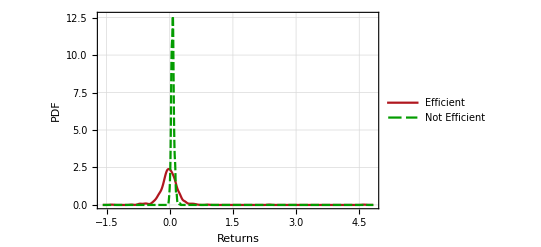

```mathematica
SmoothHistogram[{averagesFixed[[All,2]],averagesFixed[[All,3]]},
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Returns",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->Automatic,
PlotStyle->{colors[[1]],colors[[4]]},
PlotLegends->{"Efficient","Not Efficient"}
]
```

```mathematica
Mean[averagesFixed[[All,2]]]
```

-0.00303258

```mathematica
Mean[averagesFixed[[All,3]]]
```

0.0704529